# TP 2 : Tests d’hypothèses

## Travail en séance

## Données

```mathematica
data={5.5,3,13.7,13,18,11.9,9.4,10.5,15.9,9.8,8.4,8.7,18,12.7,9.4,14.4,7.3,9.3,7.7,8.4,11.2,5.5,8,11.6,6.2,5.2,18.7,9.1,13.7,9.1,8.4,9.4,6.9,8.7,11.2,8.7,5.9,8.7,9.8,19.6,9.6,14.1,9.1,13.7,6.9,8.7,7.3,9.6,13,13.5,15.2,15.7,14.4,8,9.4,6.6,10.9,8.4,9.8,18,10,18,19.3,4.1,9.8,17.3,13.7,11.6,6.6,6.9,11.9,19.9,9.8,8.4,15.2,11.4,7.7,11.9,12.3,12.7,19.9,8,11.9,13,14.3,14.4,16.6,14.1,9.4,13.7,12.7,9.8,8.4,7.7,11,6.9,4.4,10.3,18.4,8.5,11.2,13,19.9,10.7,8,13.7,19.8,10.5,13.7,3.4,5.9,4.3,8.7,10.9,11.2,9.8,9.8,10.3,6.6,12.3,7.7,10.5,11.6,8.7,8,7.7,4.4,11.6,8,9.6,9.1,12.1,10.2,13.7,12.7,13,12.3,8.4,7.3,9.6,8,9.8,7.3,14.8,7.7,9.4,13.2,9.8,13,8.7,16.9,12.3,8.7,11.6,8.4,5.2,19.9,12.1,8,9.3,13.7,6.6,13.4,5.5,8.7,6.6,12.3,12.7,10.9,7.3,8.4,19.9,8.7,9.4,16.9,18.4,11.8,7.7,8,6.2,15.2,11.9,11.6,7.7,11.2,9.1,9.8,13.4,11.2,19.9,6.8,8.2,18.4,14.4,10.9,9.8,17.3,14.3,8,13,19.9,19.9,19.9,19.14,18.55,18.55,18.42,18.29,18.22,18.16,17.83,17.63,17.63,17.37,17.24,16.84,16.32,16.18,16.18,16.18,16.05,15.92,15.92,15.79,15.79,15.66,15.66,15.66,15.66,15.66,15.53,15.53,15.39,15.39,15.39,15.39,15.26,15.13,15.13,15,15,15,15,14.93,14.87,14.74,14.74,14.61,14.61,14.61,14.61,14.34,14.21,14.21,14.08,14.08,14.08,14.08,14.08,13.95,13.82,13.82,13.82,13.68,13.62,13.55,13.42,13.42,13.42,13.29,13.16,13.16,13.16,12.89,12.89,12.89,12.89,12.89,12.89,12.76,12.76,12.76,12.76,12.63,12.5,12.5,12.5,12.5,12.43,12.37,12.37,12.37,12.24,12.24,12.24,12.24,12.24,12.24,12.11,12.11,12.11,12.11,11.97,11.97,11.84,11.84,11.84,11.84,11.84,11.58,11.58,11.58,11.58,11.58,11.45,11.45,11.25,11.25,11.25,11.18,11.18,11.05,11.05,10.92,10.92,10.83,10.79,10.79,10.66,10.66,10.66,10.66,10.53,10.53,10.53,10.53,10.53,10.39,10.39,10.39,10.26,10.26,10.26,10.26,10.26,10.13,10.13,10,10,10,10,10,10,9.87,9.84,9.74,9.74,9.74,9.74,9.67,9.61,9.61,9.61,9.41,9.34,9.34,9.34,9.28,9.21,9.21,9.08,8.95,8.95,8.82,8.82,8.82,8.68,8.55,8.42,8.29,8.29,8.16,8.03,7.89,7.89,7.63,7.63,7.5,7.43,7.24,7.11,6.97,6.97,6.84,6.84,6.84,6.84,6.71,6.71,6.58,6.45,6.32,6.18,5.66,5.39,5.39,5.26,5.26,5.13,4.61,4.61,4.47,2.63,11.45,13.16,11.05};
```

## Adéquation à une loi normale

Question 1

```mathematica
muEstim=Mean[data]
varEstim=Variance[data]
skewnessEstim=Skewness[data]
kurtoEstim=Kurtosis[data]
```

11.3792

13.0466

0.303398

2.72187

Question 2

On consulte la documentation des fonctions Mean et Variance :

On constate que la formule de muEstim fournie dans la documentation de Mathematica est identique à celle que l'on obtient dans la préparation. Toutefois, la formule de varEstim issue de Mathematica pour varEstim est différente de notre préparation, puisque le dénominateur de la formule est n-1 (au lieu de n).

Question 3

Nous savons que la loi normale est une distribution symétrique, ce qui implique d'après la préparation que le coefficient d'asymétrie sera égal à 0. Nous savons également d'après le cours que le kurtosis d'une loi normale vaut 3, ce dont nous pouvons nous assurer en calculant les valeurs :

```mathematica
LoiNormale=NormalDistribution[0,1];

kurtoLoiNormale=Kurtosis[LoiNormale]
skewnessLoiNormale=Skewness[LoiNormale]
```

3

0

Question 4

0.110449 ⅇ^(-0.0383243 (-11.3792+t)^2)

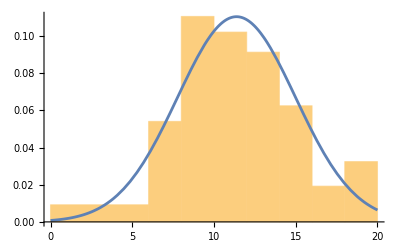

```mathematica
hist=Histogram[data,{{0,6,8,10,12,14,16,18,20}},"PDF"];
LoiNormale2=PDF[NormalDistribution[muEstim,Sqrt[varEstim]],t]
plot=Plot[LoiNormale2,{t,0,20}];
Show[hist,plot]
```

PS : Si apres compilation, la superposition des courbes de s'effectue pas, une seconde version fonctionnelle se situe en fin de TP : "Question 4 bis"

-Graphics-

Par superposition des tracés, on remarque que la distribution possède assez bien l'allure d'une loi normale.

Question 5

```mathematica
fR[x_] := CDF[NormalDistribution[muEstim,Sqrt[varEstim]],x]
Plot[fR[x], {x, -1, 25}]
```

-Graphics-

Question 6

```mathematica
effObs=BinCounts[data,{0,20,1}]
```

{0,0,1,2,7,13,24,21,44,48,42,43,41,35,25,27,9,7,14,13}

```mathematica
effTh=Table[Length[data]*(fR[i+1]-fR[i]),{i, 1, 18, 1.0}]
```

{1.1136,2.27495,4.3066,7.55472,12.2807,18.499,25.8225,33.4018,40.0374,44.4719,45.7751,43.6613,38.5912,31.6084,23.9906,16.8734,10.9973,6.64191}

On ajoute manuellement les valeurs extrêmes :

```mathematica
PrependTo[effTh, fR[1.0]]
```

{0.0020295,1.1136,2.27495,4.3066,7.55472,12.2807,18.499,25.8225,33.4018,40.0374,44.4719,45.7751,43.6613,38.5912,31.6084,23.9906,16.8734,10.9973,6.64191}

```mathematica
AppendTo[effTh,Length[data]*(1-fR[19.0])]
```

{0.0020295,1.1136,2.27495,4.3066,7.55472,12.2807,18.499,25.8225,33.4018,40.0374,44.4719,45.7751,43.6613,38.5912,31.6084,23.9906,16.8734,10.9973,6.64191,7.2533}

Question 7

```mathematica
regroupeGauche[liste_,k_]:=Prepend[Table[liste[[i]],{i,k+1,Length[liste]}],Sum[liste[[i]],{i,1,k}]]
```

```mathematica
regroupeGauche[{2,4,3,6,3,7},4]
```

{15,3,7}

Question 8

Pour utiliser le théorème de distance de Chi2, il faut que chacuns des effectifs soient supérieurs à 5, c'est pourquoi nous effectuons le regroupement des classes inférieurs à 5 avec notre fonction regroupeGauche :

```mathematica
effThBis=regroupeGauche[effTh,4]
```

{7.69718,7.55472,12.2807,18.499,25.8225,33.4018,40.0374,44.4719,45.7751,43.6613,38.5912,31.6084,23.9906,16.8734,10.9973,6.64191,7.2533}

```mathematica
effObsBis=regroupeGauche[effObs,4]
```

{3,7,13,24,21,44,48,42,43,41,35,25,27,9,7,14,13}

Question 9

```mathematica
Total[(effObsBis-effThBis)^2/effThBis]
```

30.8245

Question 10

Le nombre de degrés de liberté du problèmes est égal au nombres de classes - 1 - estimations, soit 14. Pour un risque de première espèce avec alpha = 5% on obitent le seuil suivant (aussi obtenable avec la table de Chi2 en fin de cours) :

```mathematica
seuil = InverseCDF[ChiSquareDistribution[14],0.95]
```

23.6848

On constate finalement que : seuil < Distance Chi2 (23.6848 < 30.8245). L'hypothèse nulle est donc rejetée, c'est-à-dire que l'estimation "data" ne suit pas une loi normale.

## Prise en compte de l’asymétrie

Question 11

```mathematica
plotA=Plot[PDF[SkewNormalDistribution[0,1,1],x],{x,-10,10}, PlotStyle -> Red]
plotB=Plot[PDF[NormalDistribution[0,1],x],{x,-10,10}]
Show[plotA,plotB]
```

-Graphics-

-Graphics-

-Graphics-

Question 12

```mathematica
logvraissemblance[m_, s_, a_] := Total[LogLikelihood[SkewNormalDistribution[m, s, a], data]]
```

Question 13

```mathematica
{mEstim, sEstim, aEstim} = {m, s, a} /. FindMaximum[logvraissemblance[m, s, a], {{m, 0}, {s, 1}, {a, 1}}][[2]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{7.81848,5.06894,1.83272}

Question 14

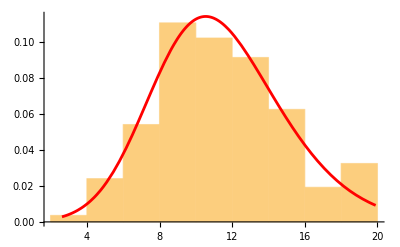

```mathematica
Show[Histogram[data, Automatic, "PDF"], Plot[PDF[SkewNormalDistribution[mEstim, sEstim, aEstim], x], {x, Min[data], Max[data]}, PlotStyle -> Red]]
```

Question 16

Nous calculons la distance de Chi2 : 
Fonction de répartition :

```mathematica
fR3[x_]:=CDF[SkewNormalDistribution[mEstim,sEstim,aEstim],x]
Plot[fR3[x],{x,-1,25}]
```

-Graphics-

Effectifs théorique (l'effectif observé reste le même puisque l'on étudie le même échantillon) :

```mathematica
effTh3=Table[Length[data]*(fR3[i+1]-fR3[i]),{i, 1, 18, 1.0}]
```

{0.354349,1.06873,2.76909,6.18435,11.9558,20.116,29.6584,38.6461,44.9697,47.2978,45.5634,40.7414,34.225,27.2725,20.7527,15.1395,10.6099,7.14926}

Ajout des valeurs extrêmes :

```mathematica
PrependTo[effTh3,Length[data]* fR3[1.0]]
```

{0.131239,0.354349,1.06873,2.76909,6.18435,11.9558,20.116,29.6584,38.6461,44.9697,47.2978,45.5634,40.7414,34.225,27.2725,20.7527,15.1395,10.6099,7.14926}

```mathematica
AppendTo[effTh3,Length[data]*(1-fR3[19.0])]
```

{0.131239,0.354349,1.06873,2.76909,6.18435,11.9558,20.116,29.6584,38.6461,44.9697,47.2978,45.5634,40.7414,34.225,27.2725,20.7527,15.1395,10.6099,7.14926,11.3949}

Regroupement des classes inférieures à 5 :

```mathematica
effThBis3=regroupeGauche[effTh3,5]
```

{10.5078,11.9558,20.116,29.6584,38.6461,44.9697,47.2978,45.5634,40.7414,34.225,27.2725,20.7527,15.1395,10.6099,7.14926,11.3949}

```mathematica
effObsBis3=regroupeGauche[effObs,5]
```

{10,13,24,21,44,48,42,43,41,35,25,27,9,7,14,13}

Distance de Chi2 :

```mathematica
Total[(effObsBis3-effThBis3)^2/effThBis3]
```

17.6749

Degrés de liberté du problèmes : 16 - 1 - 3 = 12. Pour un risque de première espèce avec alpha = 5% on obitent le seuil suivant :

```mathematica
seuil = InverseCDF[ChiSquareDistribution[12],0.95]
```

21.0261

Nous pouvons donc en conclure que : seuil > Distance Chi2 (21.0261 < 17.6749). L'hypothèse nulle est donc acceptée :  l'estimation "data" suit donc une loi normale asymétrique de paramètre mEstim, sEstim et aEstim.

## Indépendance entre deux caractères

```mathematica
dataFemmes={19.9,18.22,17.63,17.63,16.32,15.66,15.66,15.66,15.39,15.39,15.26,15,14.87,14.61,14.08,13.68,13.42,13.42,13.29,13.16,12.89,12.89,12.76,12.76,12.76,12.37,12.24,12.24,12.24,12.24,11.84,11.05,10.66,10.39,10.39,10.26,10,9.61,9.08,7.5,6.84};
dataHommes={19.9,19.9,19.14,18.55,18.55,18.42,18.29,18.16,17.83,17.37,17.24,16.84,16.18,16.18,16.18,16.05,15.92,15.92,15.79,15.79,15.66,15.66,15.53,15.53,15.39,15.39,15.13,15.13,15,15,15,14.93,14.74,14.74,14.61,14.61,14.61,14.34,14.21,14.21,14.08,14.08,14.08,14.08,13.95,13.82,13.82,13.82,13.62,13.55,13.42,13.16,13.16,12.89,12.89,12.89,12.89,12.76,12.63,12.5,12.5,12.5,12.5,12.43,12.37,12.37,12.24,12.24,12.11,12.11,12.11,12.11,11.97,11.97,11.84,11.84,11.84,11.84,11.58,11.58,11.58,11.58,11.58,11.45,11.45,11.25,11.25,11.25,11.18,11.18,11.05,10.92,10.92,10.83,10.79,10.79,10.66,10.66,10.66,10.53,10.53,10.53,10.53,10.53,10.39,10.26,10.26,10.26,10.26,10.13,10.13,10,10,10,10,10,9.87,9.84,9.74,9.74,9.74,9.74,9.67,9.61,9.61,9.41,9.34,9.34,9.34,9.28,9.21,9.21,8.95,8.95,8.82,8.82,8.82,8.68,8.55,8.42,8.29,8.29,8.16,8.03,7.89,7.89,7.63,7.63,7.43,7.24,7.11,6.97,6.97,6.84,6.84,6.84,6.71,6.71,6.58,6.45,6.32,6.18,5.66,5.39,5.39,5.26,5.26,5.13,4.61,4.61,4.47,2.63,11.45,13.16,11.05};
```

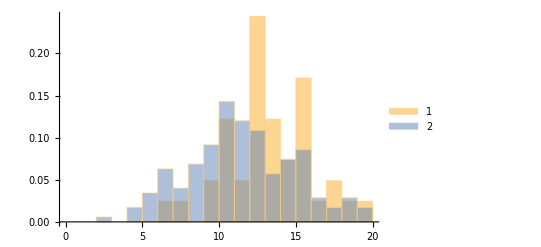

```mathematica
Histogram[{dataFemmes,dataHommes},{0,20,1},"PDF",ChartLegends->{"Femmes","Hommes"}]
```

Question 17

```mathematica
table_observes = TableForm[{{Length[dataFemmes], Length[dataHommes]}, {}}]
NbNotesHommes=BinCounts[dataHommes,{0,20,1}]
NbNotesFemmes=BinCounts[dataFemmes,{0,20,1}]
NombreFemmes=Length[dataFemmes]
NombreHommes=Length[dataHommes]
NbNotesHommes=BinCounts[dataHommes,{0,20,1}];
NbNotesFemmes=BinCounts[dataFemmes,{0,20,1}];

PrependTo[NbNotesHommes,"Hommes"];
PrependTo[NbNotesFemmes,"Femmes"];
AppendTo[NbNotesHommes,NombreHommes];
AppendTo[NbNotesFemmes,NombreFemmes];
Notes={"Tableau",0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,"Total"};
SommesChaqueNotes=Table[NbNotesFemmes[[i]]+NbNotesHommes[[i]],{i,2,21}];
PrependTo[SommesChaqueNotes,"Total"];
AppendTo[SommesChaqueNotes,total];
total=NombreFemmes+NombreHommes;

Grid[{Notes, NbNotesHommes, NbNotesFemmes, SommesChaqueNotes}, Frame->All]
```

41 | 175
 |

{0,0,1,0,3,6,11,7,12,16,25,21,19,10,13,15,5,3,5,3}

{0,0,0,0,0,0,1,1,0,2,5,2,10,5,3,7,1,2,1,1}

41

175

Tableau | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | Total
Hommes | 0 | 0 | 1 | 0 | 3 | 6 | 11 | 7 | 12 | 16 | 25 | 21 | 19 | 10 | 13 | 15 | 5 | 3 | 5 | 3 | 175
Femmes | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 5 | 2 | 10 | 5 | 3 | 7 | 1 | 2 | 1 | 1 | 41
Total | 0 | 0 | 1 | 0 | 3 | 6 | 12 | 8 | 12 | 18 | 30 | 23 | 29 | 15 | 16 | 22 | 6 | 5 | 6 | 4 | 216

Question 18

Question 19

```mathematica
observed_flat = Flatten[ observes]
expected_flat = Flatten[expected]
chiSquareDistance = Total[(observed - expected)^2 / expected]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[observes].

Flatten[observes]

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[expected].

Flatten[expected]

Total[(-expected+observed)^2/expected]

Question 20

```mathematica
alpha = 0.05; (* Niveau de signification *)
df = 1; (* Degrés de liberté *)
valeurCritique = InverseCDF[ChiSquareDistribution[df], 1 - alpha]
t = "Rejeter l'hypothèse nulle: il y a une dépendance entre le sexe et les résultats aux contrôles.";
f = "Accepter l'hypothèse nulle: il n'y a pas de dépendance entre le sexe et les résultats aux contrôles.";
If[chiSquareDistance > valeurCritique,t,f]
```

3.84146

If[Total[(-expected+observed)^2/expected]>3.84146,t,f]

Question 4 bis

PDF[NormalDistribution[11.3792,3.612],Rejeter l'hypothèse nulle: il y a une dépendance entre le sexe et les résultats aux contrôles.]

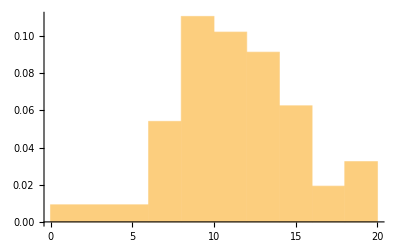

-Graphics-

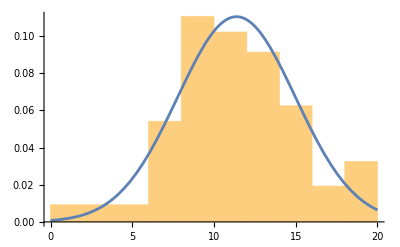

```mathematica
hist=Histogram[data,{{0,6,8,10,12,14,16,18,20}},"PDF"];
LoiNormale2=PDF[NormalDistribution[muEstim,Sqrt[varEstim]],t]
plot=Plot[LoiNormale2,{t,0,20}];
Show[hist,plot]
plot2=Plot[PDF[NormalDistribution[11.3792, 3.612], x], {x, 0, 20}, PlotRange -> All, 
    PlotLabel -> "Densité de probabilité de la distribution normale"]
    Show[hist,plot2]
```